# Constructing Term Structure -- Nelson-Siegel

## Equal Weighted

```mathematica
α = 1;
```

```mathematica
R[t_, β0_, β1_, β2_] := β0 + β1 *(1-ⅇ^(-α*t))/(α * t) + β2*(1 - (1 + α * t)*ⅇ^(-α * t))/(α * t);
```

```mathematica
B[t_, β0_, β1_, β2_] := ⅇ^(-t*R[t,β0,β1,β2]);
```

```mathematica
Cp[t_, c_, β0_, β1_, β2_] := 0.5 * ∑_(i=1)^(2*t) c * ⅇ^(-(i/2)*R[i/2,β0,β1,β2])+ ⅇ^(-t*R[t,β0,β1,β2]);
```

```mathematica
{b0, b1, b2} =  {β0,β1,β2}/.Minimize[
(1 - Cp[1, 0.54/ 100, β0, β1, β2])^2 +
(1 - Cp[2, 0.85 / 100, β0, β1, β2])^2+
(1 - Cp[5, 1.59 / 100, β0, β1, β2])^2 +(1 - Cp[10, 2.22/ 100, β0, β1, β2])^2 ,{β0, β1, β2}][[2]]
```

{0.0292219,-0.0131588,-0.0538798}

## Duration weighted

```mathematica
Dur[t_, c_, β0_, β1_, β2_] := ∑_(i=1)^(2*t) (0.5*c *(i/2) *ⅇ^(-(i/2)*R[i/2,β0,β1,β2]))/Cp[t,c,β0,β1,β2]+ (1*t*ⅇ^(-t*R[t,β0,β1,β2]))/Cp[t,c,β0,β1,β2];
```

```mathematica
{B0, B1, B2} =  {β0,β1,β2}/.Minimize[
(1/Dur[1,0.54∕100,β0,β1,β2])*(1 - Cp[1, 0.54/ 100, β0, β1, β2])^2 +
(1∕Dur[2,0.85∕100,β0,β1,β2])*(1 - Cp[2, 0.85 / 100, β0, β1, β2])^2+
(1∕Dur[5, 1.59∕100,β0,β1,β2])*(1 - Cp[5, 1.59 / 100, β0, β1, β2])^2 +(1∕Dur[10, 2.22∕100,β0,β1,β2])*(1 - Cp[10, 2.22/ 100, β0, β1, β2])^2 ,{β0, β1, β2}][[2]]
```

{0.0286729,-0.016788,-0.046042}

## Plot

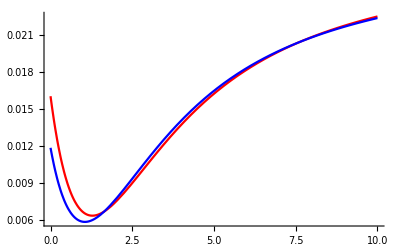

```mathematica
Plot[{R[t,b0,b1,b2],R[t,B0,B1,B2]},{t,0,10},PlotStyle->{Red,Blue}]
```

```mathematica
ClearAll
```

ClearAll